```mathematica
"definição do estádio"
a=1
b=1
```

definição do estádio

1

1

```mathematica
"definição da base utilizada"
φ[x_,y_,n_,m_]=(x+√(y(b-y)))^n(x-a-√(y(b-y)))y^m(y-b)
nM=3
mM=3
Base[x_,y_]=Table[φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM],{i,0,nM*mM-1}]
```

definição da base utilizada

(-1+y) y^m (-1+x-√((1-y) y)) (x+√((1-y) y))^n

3

3

{(-1+y) y (-1+x-√((1-y) y)) (x+√((1-y) y)),(-1+y) y (-1+x-√((1-y) y)) (x+√((1-y) y))^2,(-1+y) y (-1+x-√((1-y) y)) (x+√((1-y) y))^3,(-1+y) y^2 (-1+x-√((1-y) y)) (x+√((1-y) y)),(-1+y) y^2 (-1+x-√((1-y) y)) (x+√((1-y) y))^2,(-1+y) y^2 (-1+x-√((1-y) y)) (x+√((1-y) y))^3,(-1+y) y^3 (-1+x-√((1-y) y)) (x+√((1-y) y)),(-1+y) y^3 (-1+x-√((1-y) y)) (x+√((1-y) y))^2,(-1+y) y^3 (-1+x-√((1-y) y)) (x+√((1-y) y))^3}

```mathematica
"definição da matriz A"
A[k_] =Table[NIntegrate[φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM]Laplacian[φ[x,y,1+Mod[j,nM],1+(j-Mod[j,nM])/mM],{x,y}],{y,0,b},{x,-√(y(b-y)),a+√(y(b-y))},AccuracyGoal->∞]+k^2 NIntegrate[φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM]φ[x,y,1+Mod[j,nM],1+(j-Mod[j,nM])/mM],{y,0,b},{x,-√(y(b-y)),a+√(y(b-y))},AccuracyGoal->∞],{i,0,nM*mM-1},{j,0,nM*mM-1}]
A[k] // MatrixForm
```

definição da matriz A

{{-0.400326+0.0297346 k^2,-0.39551+0.0288646 k^2,-0.453456+0.032073 k^2,-0.200163+0.0148673 k^2,-0.197755+0.0144323 k^2,-0.226728+0.0160365 k^2,-0.105524+0.00823435 k^2,-0.104676+0.00795602 k^2,-0.12008+0.00880239 k^2},{-0.39551+0.0288646 k^2,-0.487975+0.032073 k^2,-0.638811+0.0390344 k^2,-0.197755+0.0144323 k^2,-0.243988+0.0160365 k^2,-0.319406+0.0195172 k^2,-0.100817+0.00795602 k^2,-0.126375+0.00880239 k^2,-0.166553+0.0106705 k^2},{-0.453456+0.032073 k^2,-0.638811+0.0390344 k^2,-0.919712+0.0507389 k^2,-0.226728+0.0160365 k^2,-0.319406+0.0195172 k^2,-0.459856+0.0253695 k^2,-0.113018+0.00880239 k^2,-0.162844+0.0106705 k^2,-0.23702+0.0138195 k^2},{-0.200163+0.0148673 k^2,-0.197755+0.0144323 k^2,-0.226728+0.0160365 k^2,-0.135259+0.00823435 k^2,-0.131611+0.00795602 k^2,-0.148622+0.00880239 k^2,-0.0879395+0.00491788 k^2,-0.0850718+0.00471788 k^2,-0.0952976+0.00518532 k^2},{-0.197755+0.0144323 k^2,-0.243988+0.0160365 k^2,-0.319406+0.0195172 k^2,-0.131611+0.00795602 k^2,-0.158448+0.00880239 k^2,-0.203733+0.0106705 k^2,-0.0831423+0.00471788 k^2,-0.0996413+0.00518532 k^2,-0.127307+0.00624722 k^2},{-0.226728+0.0160365 k^2,-0.319406+0.0195172 k^2,-0.459856+0.0253695 k^2,-0.148622+0.00880239 k^2,-0.203733+0.0106705 k^2,-0.287759+0.0138195 k^2,-0.0917667+0.00518532 k^2,-0.125452+0.00624722 k^2,-0.176341+0.00804453 k^2},{-0.105524+0.00823435 k^2,-0.100817+0.00795602 k^2,-0.113018+0.00880239 k^2,-0.0879395+0.00491788 k^2,-0.0831423+0.00471788 k^2,-0.0917667+0.00518532 k^2,-0.0659503+0.00311323 k^2,-0.0620146+0.00296158 k^2,-0.0678378+0.00322944 k^2},{-0.104676+0.00795602 k^2,-0.126375+0.00880239 k^2,-0.162844+0.0106705 k^2,-0.0850718+0.00471788 k^2,-0.0996413+0.00518532 k^2,-0.125452+0.00624722 k^2,-0.0620146+0.00296158 k^2,-0.0718884+0.00322944 k^2,-0.0895758+0.00386212 k^2},{-0.12008+0.00880239 k^2,-0.166553+0.0106705 k^2,-0.23702+0.0138195 k^2,-0.0952976+0.00518532 k^2,-0.127307+0.00624722 k^2,-0.176341+0.00804453 k^2,-0.0678378+0.00322944 k^2,-0.0895758+0.00386212 k^2,-0.122742+0.00493881 k^2}}

(-0.400326+0.0297346 k^2 | -0.39551+0.0288646 k^2 | -0.453456+0.032073 k^2 | -0.200163+0.0148673 k^2 | -0.197755+0.0144323 k^2 | -0.226728+0.0160365 k^2 | -0.105524+0.00823435 k^2 | -0.104676+0.00795602 k^2 | -0.12008+0.00880239 k^2
-0.39551+0.0288646 k^2 | -0.487975+0.032073 k^2 | -0.638811+0.0390344 k^2 | -0.197755+0.0144323 k^2 | -0.243988+0.0160365 k^2 | -0.319406+0.0195172 k^2 | -0.100817+0.00795602 k^2 | -0.126375+0.00880239 k^2 | -0.166553+0.0106705 k^2
-0.453456+0.032073 k^2 | -0.638811+0.0390344 k^2 | -0.919712+0.0507389 k^2 | -0.226728+0.0160365 k^2 | -0.319406+0.0195172 k^2 | -0.459856+0.0253695 k^2 | -0.113018+0.00880239 k^2 | -0.162844+0.0106705 k^2 | -0.23702+0.0138195 k^2
-0.200163+0.0148673 k^2 | -0.197755+0.0144323 k^2 | -0.226728+0.0160365 k^2 | -0.135259+0.00823435 k^2 | -0.131611+0.00795602 k^2 | -0.148622+0.00880239 k^2 | -0.0879395+0.00491788 k^2 | -0.0850718+0.00471788 k^2 | -0.0952976+0.00518532 k^2
-0.197755+0.0144323 k^2 | -0.243988+0.0160365 k^2 | -0.319406+0.0195172 k^2 | -0.131611+0.00795602 k^2 | -0.158448+0.00880239 k^2 | -0.203733+0.0106705 k^2 | -0.0831423+0.00471788 k^2 | -0.0996413+0.00518532 k^2 | -0.127307+0.00624722 k^2
-0.226728+0.0160365 k^2 | -0.319406+0.0195172 k^2 | -0.459856+0.0253695 k^2 | -0.148622+0.00880239 k^2 | -0.203733+0.0106705 k^2 | -0.287759+0.0138195 k^2 | -0.0917667+0.00518532 k^2 | -0.125452+0.00624722 k^2 | -0.176341+0.00804453 k^2
-0.105524+0.00823435 k^2 | -0.100817+0.00795602 k^2 | -0.113018+0.00880239 k^2 | -0.0879395+0.00491788 k^2 | -0.0831423+0.00471788 k^2 | -0.0917667+0.00518532 k^2 | -0.0659503+0.00311323 k^2 | -0.0620146+0.00296158 k^2 | -0.0678378+0.00322944 k^2
-0.104676+0.00795602 k^2 | -0.126375+0.00880239 k^2 | -0.162844+0.0106705 k^2 | -0.0850718+0.00471788 k^2 | -0.0996413+0.00518532 k^2 | -0.125452+0.00624722 k^2 | -0.0620146+0.00296158 k^2 | -0.0718884+0.00322944 k^2 | -0.0895758+0.00386212 k^2
-0.12008+0.00880239 k^2 | -0.166553+0.0106705 k^2 | -0.23702+0.0138195 k^2 | -0.0952976+0.00518532 k^2 | -0.127307+0.00624722 k^2 | -0.176341+0.00804453 k^2 | -0.0678378+0.00322944 k^2 | -0.0895758+0.00386212 k^2 | -0.122742+0.00493881 k^2)

```mathematica
"autovalores obtidos numericamente"
NSolve[Det[A[k]]== 0 && k ≥ 0,k]
```

autovalores obtidos numericamente

{{k→3.59471},{k→4.78595},{k→6.37402},{k→6.60703},{k→7.72397},{k→9.28037},{k→9.71569},{k→10.7648},{k→12.3234}}

```mathematica
"autofunções(para um dado autovalor ka) obtidas numericamente: id é um indice de degenerescencia"
ka=12.323388008404736
Vc[ka]=NullSpace[A[ka]]
id=1
v=Vc[ka][[id]]
ϕ[x_,y_]=Base[x,y].v
```

autofunções(para um dado autovalor ka) obtidas numericamente: id é um indice de degenerescencia

12.3234

{}

1

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

{(-1+y) y (-1+x-√((1-y) y)) (x+√((1-y) y)),(-1+y) y (-1+x-√((1-y) y)) (x+√((1-y) y))^2,(-1+y) y (-1+x-√((1-y) y)) (x+√((1-y) y))^3,(-1+y) y^2 (-1+x-√((1-y) y)) (x+√((1-y) y)),(-1+y) y^2 (-1+x-√((1-y) y)) (x+√((1-y) y))^2,(-1+y) y^2 (-1+x-√((1-y) y)) (x+√((1-y) y))^3,(-1+y) y^3 (-1+x-√((1-y) y)) (x+√((1-y) y)),(-1+y) y^3 (-1+x-√((1-y) y)) (x+√((1-y) y))^2,(-1+y) y^3 (-1+x-√((1-y) y)) (x+√((1-y) y))^3}.{}⟦1⟧

```mathematica
"esboço da autofunção obtida"
Plot3D[ϕ[x,y],{x,-b/2,a+(b/2)},{y,0,b},RegionFunction->Function[{x,y,z},-√(y(b-y))≤ x≤a+√(y(b-y))]]
```

esboço da autofunção obtida

-Graphics3D-

curvas de nível da autofunção

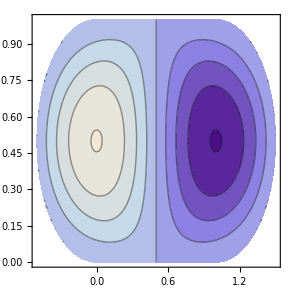

```mathematica
"curvas de nível da autofunção"
ContourPlot[ϕ[x,y],{x,-b/2,a+(b/2)},{y,0,b},RegionFunction->Function[{x,y,z},-√(y(b-y))≤ x≤a+√(y(b-y))]]
```

linhas nodais da autofunção

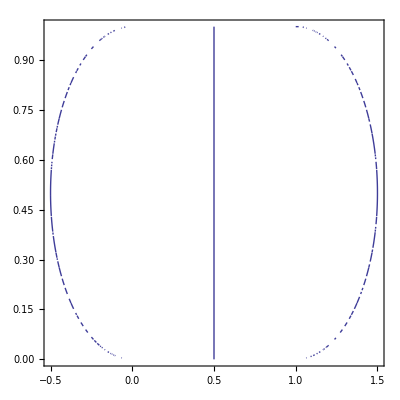

```mathematica
"linhas nodais da autofunção"
ContourPlot[ϕ[x,y]== 0,{x,-b/2,a+(b/2)},{y,0,b},RegionFunction->Function[{x,y,z},-√(y(b-y))≤ x≤a+√(y(b-y))]]
```